# +

—Clayton Shonkwiler, June 2025

Recall that the Riemannian metric on the Poincaré half-plane model of the hyperbolic plane ℍ^2 is ⅆ s^2=1/y^2(ⅆ x^2+ⅆ y^2), which means that the inner product of two tangent vectors  U=u_1∂/(∂x)+u_2∂/(∂y),V=v_1∂/(∂x)+v_2∂/(∂x)∈T_(x,y)ℍ^2 is

	⟨U,V⟩_(x,y)=(u_1 v_1)/y^2+(u_2 v_2)/y^2=1/y^2(u_1 v_1+u_2 v_2).

As in the notebook for my animation Parallels (Github version), use the notation X=∂/(∂x) and Y=∂/(∂y) and observe that 

	∇_X X=1/y Y,	∇_X Y=∇_Y X=-1/yX, 		∇_Y Y=-1/yY.

For more details, see Example 4.3.10 in my differential geometry notes.

The curve γ(t)=(0,ⅇ^t) is a unit-speed geodesic in the hyperbolic metric: it’s unit-speed since 

	⟨γ'(t),γ'(t)⟩_(γ(t))=⟨ⅇ^t Y,ⅇ^t Y⟩_(0,ⅇ^t)=1/ⅇ^(2t)ⅇ^(2t)=1
	
and in this case the geodesic equation reduces to y''=(y')^2/y, which is certainly satisfied by y(t)=ⅇ^t.

Therefore, the distance from (0,y_1)=γ(ln(y_1)) to (0,y_2)=γ(ln(y_2)) is exactly ln(y_2)-ln(y_1)=ln(y_2/y_1), and hence the following horizontal lines (which are horocycles centered at ∞) are equally-spaced:

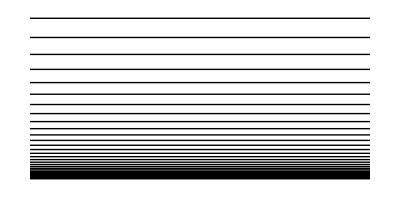

```mathematica
Graphics[Table[InfiniteLine[{{0,E^t},{1,E^t}}],{t,-4,0,1/8}],PlotRange->{{-1,1},{0,1}}]
```

In the Parallels notebook, I worked out what parallel translation looks like for horocycles α(t)=(y_0 t,y_0). For example, if I paralle translate a pair of perpendicular lines along one of these curves it looks something like this:

```mathematica
With[{y0=1/2.},
Animate[Graphics[{CapForm["Round"],ParallelTable[{
Thickness[.003],
Line[{{y0 s,y0}-y0/16{Sin[s/y0],Cos[s/y0]},{y0 s,y0}+y0/16{Sin[s/y0],Cos[s/y0]}}],Line[{{y0 s,y0}-y0/16{Sin[s/y0+π/2],Cos[s/y0+π/2]},{y0 s,y0}+y0/16{Sin[s/y0+π/2],Cos[s/y0+π/2]}}]},{s,-π+t,π+t,2π/30}]},PlotRange->{{-1,1},{0,1}},Axes->True,ImageSize->540],{t,0.,2π/30},SaveDefinitions->True,AnimationRate->1]
]
```

Now, play the same game as in Parallels, where we transformed this horocycle into one centered at a different point by applying the Cayley transform, rotating (this time multiplying by -1 rather than -ⅈ), then applying the inverse Cayley transform. Again, we’ll scale the thickness by the height to that the plus symbols are of constant size in the hyperbolic metric.

```mathematica
Cayley[z_]:=(z-I)/(z+I);
CayleyInverse[z_]:=I(1+z)/(1-z);
```

```mathematica
With[{y0=1/2.},
Animate[Graphics[{CapForm["Round"],ParallelTable[{
Thickness[1/(y0(1+s^2))*.005],
Line[{ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}-y0/16{Sin[s/y0],Cos[s/y0]})]]],ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}+y0/16{Sin[s/y0],Cos[s/y0]})]]]}],Line[{ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}-y0/16{Sin[s/y0+π/2],Cos[s/y0+π/2]})]]],ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}+y0/16{Sin[s/y0+π/2],Cos[s/y0+π/2]})]]]}]},{s,-4π+t,4π+t,2π/30}]},PlotRange->{{-2.5,2.5},{0,2.5}},Axes->True,ImageSize->540],{t,0.,2π/30},SaveDefinitions->True,AnimationRate->1]
]
```

Of course, we want to do a bunch of parallel, equidistant horocycles, not just one. And we also want to assign each horocycle a different color from some nice color gradient.

For the colors, we’ll use the bubblegum colormap from CMasher:

```mathematica
bubblegum=RGBColor/@Import["https://raw.githubusercontent.com/1313e/CMasher/refs/heads/master/src/cmasher/colormaps/bubblegum/bubblegum_norm.txt","Table"];
```

Using a linear gradient doesn’t look very good, since most of the horocycles end up quite (visually) small, so instead we’ll use a cubic easing function from Daniel Sanchez’s excellent EasingFunction resource function:

```mathematica
ease=ResourceFunction["EasingFunction"]["InCubic"];
```

The result is a little too heavy for a dynamic animation, but here’s a static image:

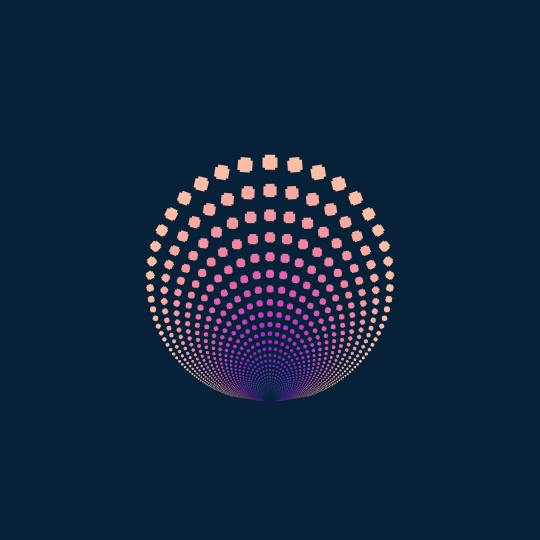

```mathematica
Module[{y0,t=0.},
Graphics[{CapForm["Round"],ParallelTable[{y0=E^h;
Thickness[1/(y0(1+s^2))*.005],
Blend[bubblegum,ease[1-(h+1)/6]],Line[{ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}-y0/32{Sin[s/y0],Cos[s/y0]})]]],ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}+y0/32{Sin[s/y0],Cos[s/y0]})]]]}],Line[{ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}-y0/32{Sin[s/y0+π/2],Cos[s/y0+π/2]})]]],ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}+y0/32{Sin[s/y0+π/2],Cos[s/y0+π/2]})]]]}]},{h,-1,5,1/8},{s,-2π+t,2π+t,2π/60}]},PlotRange->{{-2.5,2.5},{-1,4}},Background->bubblegum[[1]],ImageSize->540]
]
```

By only letting the parameter run from -2π to 2π, I’m missing the bottom fraction of each horocycle. For the small ones this isn’t noticeable, but for the outer few you can actually see this in the image above. So for the final GIF I went from -20π to 20π just to be safe (as a result, this took a little while to render). Of course, I’m still missing a fraction of each horocycle, but visually this is too small to be noticeable.

```mathematica
plus=Module[{y0},
ParallelTable[Graphics[{CapForm["Round"],Table[{y0=E^h;
Thickness[1/(y0(1+s^2))*.005],
Blend[bubblegum,ease[1-(h+1)/6]],Line[{ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}-y0/32{Sin[s/y0],Cos[s/y0]})]]],ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}+y0/32{Sin[s/y0],Cos[s/y0]})]]]}],Line[{ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}-y0/32{Sin[s/y0+π/2],Cos[s/y0+π/2]})]]],ReIm[CayleyInverse[-1*Cayley[Complex@@({y0 s,y0}+y0/32{Sin[s/y0+π/2],Cos[s/y0+π/2]})]]]}]},{h,-1,5,1/8},{s,-20π+t,20π+t,2π/60}]},PlotRange->{{-2.5,2.5},{-1,4}},Background->bubblegum[[1]],ImageSize->270],{t,0.,2π/60-#,#}]&[2π/1800.]
];
```

```mathematica
Export[NotebookDirectory[]<>"plus.gif",plus,"AnimationRepetitions"->Infinity,"DisplayDurations"->1/50];
```